## Official lattice

S-band longitudinal wakes from official MAD8 lattice: https://www.slac.stanford.edu/cgi-bin/cvsweb/optics/etc/lattice/facet2/sband_l.dat?cvsroot=LCLS

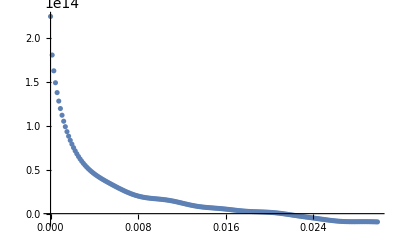

```mathematica
raw = Import["~/Downloads/sband_l.dat"];
raw=raw[[2;;]];

ListPlot[raw[[All,{2,3}]],PlotRange->All]
```

-Graphics-

## Bmad

(base) nmajik@dhcp-visitor-216-95 wakefields % cat longitudinal_wakes_sband.bmad 
! Adapted from file: 	elegant/Sz_p5um_10mm_per35mm_cell.sdds
! Usage: 
! ele[sr_wake] = call::longitudinal_wakes_sband.bmad

{
  scale_with_length = T, 
  longitudinal = {1.0214527206425931e14, 200.737972823806, 0, 0.25, none},
  longitudinal = {2.0264683145205535e13, 164752.58575866005, 0, 0.25, none},
  longitudinal = {9.111515497722739e13, 1206.8246815698092, 0, 0.25, none},
  longitudinal = {4.95817609185586e13, 9050.772842025624, 0, 0.25, none},
z_max = 0.01}

```mathematica
wakeSpecs = {
{1.02*^14, 200.737972823806},
{2.02*^13,164752.58575866005},
{9.11*^13,1206.8246815698092},
{4.96*^13,9050.772842025624}
};
```

-Graphics-

So it appears that the data file has no frequency terms! Is it just building up the wake from exponentials?

```mathematica
wakeExprs = #[[1]]*Exp[-#[[2]]*z]&/@wakeSpecs;
```

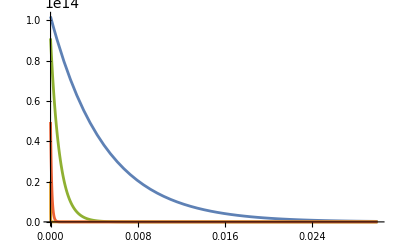

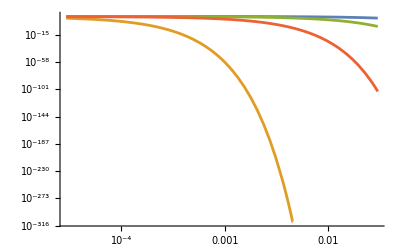

```mathematica
Plot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
LogLogPlot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
```

```mathematica
wakeSumExpr = Total[wakeExprs];
```

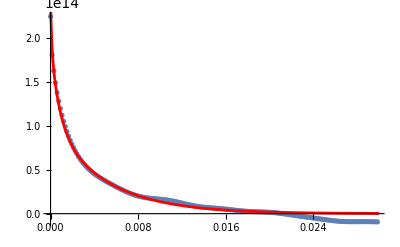

```mathematica
Show[
ListPlot[raw[[All,{2,3}]],PlotRange->All],
Plot[
wakeSumExpr,{z,0,0.03},
PlotRange->All,
PlotStyle->Red
]
]
```

Not bad! And the Bmad file specifies z_max = 0.01 and the agreement really is quite good up to that point

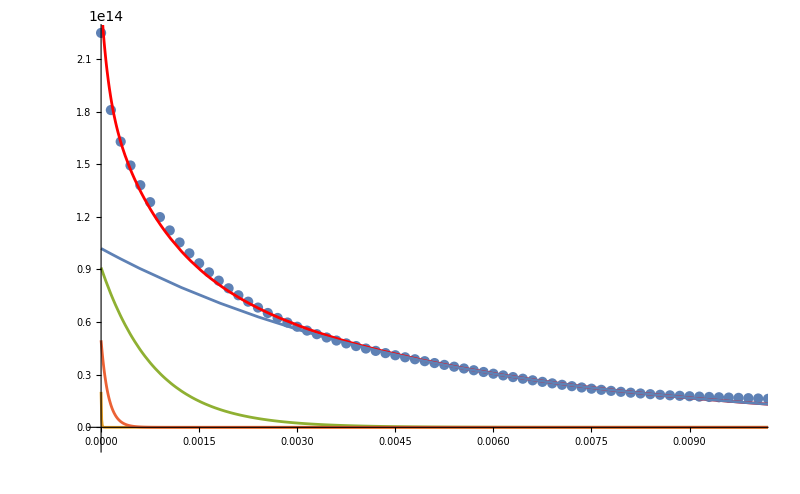

```mathematica
Show[
ListPlot[raw[[All,{2,3}]],PlotRange->{{0,0.01},All},ImageSize->800],
Plot[
wakeSumExpr ,{z,0,0.03},
PlotRange->All,
PlotStyle->Red
],
Plot[
wakeExprs,{z,0,0.03},
PlotRange->All
]
]
```

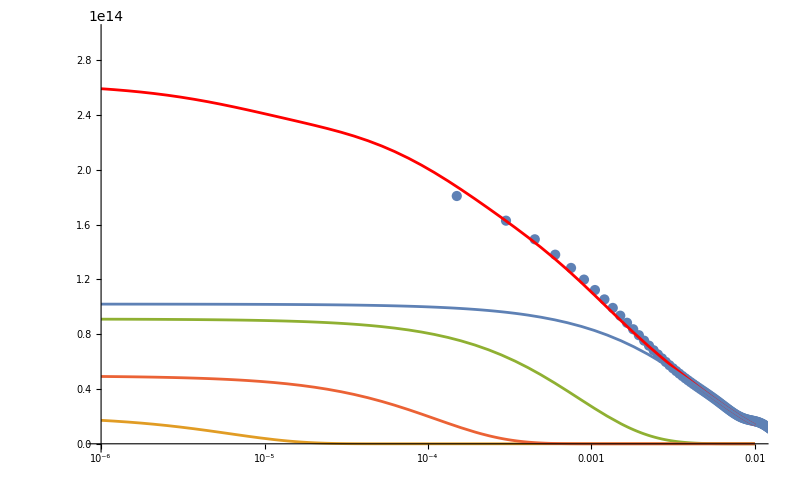

```mathematica
Show[
ListLogLinearPlot[raw[[All,{2,3}]],PlotRange->{{1*^-6,0.01},{0,3*^14}},ImageSize->800],
LogLinearPlot[
wakeSumExpr ,{z,1*^-6,0.01},
PlotRange->All,
PlotStyle->Red
],
LogLinearPlot[
wakeExprs,{z,1*^-6,0.01},
PlotRange->All
]
]
```